# 2. izpit – Mathematica

## Računalniški praktikum 2023/24

Študijske smeri: Finančna matematika, Matematika, Pedagoška matematika

## Podatki o študentu

Vpišite svoje podatke

Ime:

Priimek:

Vpisna številka:

## Navodila

Čas reševanja za celoten izpit je 120 minut.
V tem delu izpita so tri naloge, ki so skupaj vredne 30 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.
Dovoljeno je uporabljati dokumentacijo o Mathematici in gradivo iz vaj.
Vsakršna komunikacija je prepovedana.

## 1. naloga [5 točk]

Preverite, da velja enakost . 
 pomeni prodkut členov, tako kot  pomeni vsota členov. Pomagajte si z ukazom Product. Spomnite se tudi, da smo na vajah enakosti preverjali tako, da smo uporabili funkcijo za poenostavitev izrazov.

```mathematica
Simplify[Product[(1-1/k^2),{k,2,n}]]
```

(1+n)/(2 n)

## 2. naloga [15 točk]

1. (5 točk) Definirajte funkcijo f s predpisom f(x)= in izračunajte njen odvod  f'(x).
2. (5 točk) Poiščite stacionarne točke funkcije f (ničle njenega odvoda) in območje, na katerem je drugi odvod pozitiven: f''(x) > 0.
3. (5 točk) Narišite grafe f, f' in f'' na istem koordinatnem sistemu na intervalu [-3,3]. 
Stacionarni točki na grafu funkcije f označite s pomočjo predpisa Epilog (točki se bosta bolje videli, če boste uporabili tudi PointSize[Large]).

(-4 x+3 x^2)/(-1+x^2)-(2 x (1-2 x^2+x^3))/((-1+x^2)^2)

{-2,0}

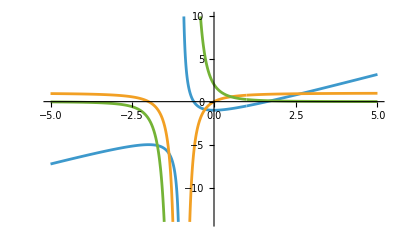

```mathematica
f[x_]:=(x^3-2 x^2+1)/(x^2-1)
f'[x]
x/.Solve[f'[x]==0]
Plot[{f[x],f'[x],f''[x]},{x,-5,5},PlotRange->Automatic]
```

## 3. naloga [10 točk]

1. (5 točk) Definirajte funkcijo koeficienti, ki sprejme parameter n in vrne seznam binomskih koeficientov .
Primer: koeficienti[5] naj vrne {1,5,10,10,5,1}. 
2. (5 točk) Nekatere matematike zanima (ker je to povezano z generiranjem alternirajočih grup), kateri binomski koeficienti so deljivi z določenimi velikimi praštevili. 
Izpišite seznam vseh binomskih koeficientov števila 31416, ki so deljivi s praštevilom 7853. Ta izračun bo nekaj časa trajal; za začetek lahko preizkusite število 210 in praštevilo 199. Lahko si pomagate s pomožno funkcijo (lahko uporabite funkcijo Divisible).

```mathematica
ClearAll[PetQ]
koeficienti[n_]:=Binomial[n,Range[0,n]]
Select[koeficienti[31416],Divisible[#,7853]&]
```